```mathematica
ClearAll["`*"]
$HistoryLength=5;
RunScheduledTask[NotebookSave[EvaluationNotebook[]],5000];
```

## System Definition

```mathematica
nAA=20;(*Number of amino-acid species*)
tmax=10000.;(*Maximal time for dynamic simulation*)
cellVolume=2.5*10^-15(*Cell volume*);
nAvogadro=6*10^23(*Avagado number*);
proteinContent=15*10^8(*aa/Cell: Bremer Dennis 1996*);
```

### Chemical species and parameters in the model

Chemical species related to aa-synthesis

```mathematica
csI={
aa,(*amino-acids*)
taa,(*charged tRNA*)
tf,(*uncharged tRNA*)
e,(*Enzyme catalyzing amino-acid synthesis*)
sTot,(*Enzyme catalyzing aa-tRNA synthase*)
rtf,(*Ribosome with uncharged tRNA in A-site*)
rf (*Ribosome with "free" A-site*)
};
```

Rate equations related to aa-synthesis

```mathematica
vI={
vAAsynt,(*Amino-acid synthesis*)
vtRNAchar(*rate of aa-tRNA synthase*)
};
```

Parameters related to amino-acid synthesis

```mathematica
parI={
(*vAAsynth*)
kn,(*kcat of amino-acid synthesis*)
kIa, (*kI of amino-acids for am*)
(*vtRNAchar*)
ks,(*kcat of aa-tRNA synthase*)
kMaa,(*kM of amino acids*)
kMtf(*kM of uncharged tRNA*),
(*other*)
f(*Fraction of amino-acid in biomass composition*),
τ(*Ratio tRNAi/ribosome*)
};
```

```mathematica
(*Function to appand index to variables and parameters
Input: index number*)
appendI[i_]:=#->ToExpression[ToString[#]<>ToString[i]]&/@Join[csI,vI,parI]
(*Append index for all AA species *)
appendAllI:=appendI[#]&/@Range[nAA]
```

Independent variables

```mathematica
(*amino acids*)
aaSpecies=aa/.appendI[#]&/@Range[nAA];
(*Charged tRNAs: taa*)
taaSpecies=taa/.appendI[#]&/@Range[nAA];
```

```mathematica
varsNoRegulation=Join[
aaSpecies,
taaSpecies
];
varsQSS=Join[
varsNoRegulation,
{ppGpp}
];
vars=Join[
varsNoRegulation,
{r,ppGpp}
];
```

Dependent variables (uncharged tRNAs)

```mathematica
(*Free/uncharged tRNAs: tf*)
tfSpecies =tf/.appendI[#]&/@Range[nAA];
depVars=tfSpecies;
```

```mathematica
tTot=Total[r*τ/.appendAllI];
```

```mathematica
rtfSpecies=rtf/.appendAllI;
```

```mathematica
rfSpecies=rf/.appendAllI;
```

### Rate equations

#### Amino-acids metabolism and protein synthesis

Rate equations of amino acid synthesis:
vi = kmi * ei * (1-r) *1/(1+ai/ki),

```mathematica
ratesAAsynt=(vAAsynt-> kn e bm/nAmet(1-r[t]/rmax)1/(1+aa[t]/kIa))/.appendAllI;
```

Rate equations for tRNA charging:

```mathematica
ratestRNAchar=vtRNAchar-> ks*sTot*(tf/kMtf*aa[t]/kMaa)/(aa[t]/kMaa+tf/kMtf+aa[t]/kMaa tf/kMtf)/.appendAllI;
```

#### Polypetide and ribosome synthesis

Rate of polypetide synthesis

```mathematica
numeratorRibosome=Simplify[1+Total[f*(κrta/taa[t]+tf/taa[t]*κrta/κrt)/.appendAllI]];
```

```mathematica
vR= (krib*r[t])/numeratorRibosome;
μ=(*conversion from per s to per hour*)(vR(*M amino acids/s*))/(bm(*M amino acids*));
```

```mathematica
drate=3600(μ/.x_[t]->x)/Log[2];(*Conver specific growth rate to doubling rate*)
```

```mathematica
vrrnInit=vInitMax*rnapF/(kMrrn+rnapF)*1/(1+(ppGpp[t]/kIppGpp)^nppGpp)*(1(*convert Nrib to Molar*))/(cellVolume*nAvogadro/10^6); (*rate of rrn transcription initiation*)
```

```mathematica
ratesGrowth={
vribosome->vR(*in aa/s*),
vRsynt->Min[vrrnInit,γmax vR/nARib],(*Rate of ribosome synthesis*)
vRdilution->r[t]*μ(*Dilution rate per second*)
};
```

```mathematica
rtfSolutions=rtf-> r[t]*(f*tf/taa[t] κrta/κrt)/numeratorRibosome/.appendAllI;(*Calculate concentration of each uncharged tRNA*)
```

```mathematica
rfSolution=rf-> (f*κrta/taa[t])/numeratorRibosome/.appendAllI;
```

```mathematica
rtfTot=Simplify[Total[rtfSpecies/.rtfSolutions]];(*Sum of all concentration of uncharged tRNA*)
```

```mathematica
ratesppGpp={
vRelA-> kRelA*RelAtot*1/(1+kDRelA/rtfTot),(*[RelA] saturating*)
vSpoTdeg->kSpoTdeg*ppGpp[t]};
```

```mathematica
ClearAll[rates]
rates=Join[
ratestRNAchar,
ratesAAsynt,
ratesGrowth,
ratesppGpp
];
```

### Odes

ODEs for amino acid species:
ai’ = vAAsynti - vtRNAchari

```mathematica
odesAA=(aa'[t]==vAAsynt-vtRNAchar)/.appendAllI;
```

ODEs for tRNA charging
tRNAaa’ = vtRNAchari - fi vribosome

```mathematica
odesTAA=taa'[t]==vtRNAchar-f*vribosome/.appendAllI;
```

ODEs for ppGpp metabolism

```mathematica
ClearAll[odesNoRegulation]
odesNoRegulation=Join[
odesAA,odesTAA
];
```

```mathematica
odesppGpp={ppGpp'[t]==vRelA +vSpoTSynt - vSpoTdeg };
```

ODEs for macromolecular composition

```mathematica
odesMacromolComp={r'[t] == vRsynt - vRdilution};
```

```mathematica
odesQSS=Join[odesNoRegulation,odesppGpp];
```

```mathematica
odes=Join[
odesNoRegulation,
odesppGpp,
odesMacromolComp];
```

### Relations between dependent variables

Total amount of each tRNA species. Neglect fraction the is bound to ribosome. This fraction is small and also relatively constant (if κrta=κrt, it is constant)

```mathematica
tmpRelations=Solve[
τ*r[t]==tf+taa[t]/.appendI[#]&/@Range[nAA],
tfSpecies];
tmpRelations//Length
relations=Flatten[tmpRelations];
Clear[tmpRelations]
```

1

### Parameters

```mathematica
pars={(*Amino-acid synthesis*)
e-> .05,
kn->.5,
kIa->10^2,
(*tRNA-aa synthese*)
sTot->1,
ks->100,
kMaa->100,(*ksi/kai in Elf and Ehrenberg, 2005*)
kMtf->1,(*KSi in Elf and Eherenberg, 2005*)

(*protein elongation*)
krib->20,
κrta->1,
κrt->500,

(*ppGpp synthesis*)
kRelA->(*4500./60*)75,(*cf. Jenvert , Schiavone, FEBS Journal 2005*)
RelAtot->(100(*100 per cell*))/(nAvogadro*cellVolume/10^6),
kDRelA->2.6*10^-1,
vSpoTSynt->.001,
kSpoTdeg->Log[2.]/30,(*Half life time of 120s: Literature value suggests 120-150s, but this gives rise to ppGpp levels not consistent with Subscript[k, IppGpp]*)

(*Ribosome synthesis*)
vInitMax-> 2000,(*Estimatied from Klumpp, Hwa *)
rnapF->1.(*Klumpp, Hwa 2008*),
kMrrn->20(*Klumpp, Hwa 2008*),
kIppGpp->1.(*1 μM, Paul et al, 2004*),
nppGpp->1.,
γmax->1.(*Maximal fraction of ribosome capacity dedicated to ribosome synthesis*),
(*other*)
τ->.5,(*tRNAi/r*)
f->1/20.,
bm->proteinContent/(cellVolume*nAvogadro/10^6)(*Biomass concentration in Molar amino-acids*),
nARib->7459(*aa/ribosome: BNID 101175*)*1.65(*Ratio "extended ribosome"/ribosome*),
nAmet-> 300(*Avarage size of a protein*),
rmax-> proteinContent/(cellVolume*nAvogadro/10^6)/(7459*1.65)(*ribosomal concentratation when all biomass is ribosome. Equivalent to [total protein] and p*)
}/.appendAllI//Flatten//DeleteDuplicates;
SeedRandom[0]
pars=pars/.(Rule[#->_,#->fac*RandomVariate[LogNormalDistribution[Log[1.],.2]]]&/@(kn/.appendAllI));
pars=pars/.fac->0.2
```

{e1→0.05,kn1→0.176694,kIa1→100,sTot1→1,ks1→100,kMaa1→100,kMtf1→1,krib→20,κrta→1,κrt→500,kRelA→75,RelAtot→0.0666667,kDRelA→0.26,vSpoTSynt→0.001,kSpoTdeg→0.0231049,vInitMax→2000,rnapF→1.,kMrrn→20,kIppGpp→1.,nppGpp→1.,γmax→1.,τ1→0.5,f1→0.05,bm→1.×10^6,nARib→12307.3,nAmet→300,rmax→81.2523,e2→0.05,kn2→0.170472,kIa2→100,sTot2→1,ks2→100,kMaa2→100,kMtf2→1,τ2→0.5,f2→0.05,e3→0.05,kn3→0.215015,kIa3→100,sTot3→1,ks3→100,kMaa3→100,kMtf3→1,τ3→0.5,f3→0.05,e4→0.05,kn4→0.16053,kIa4→100,sTot4→1,ks4→100,kMaa4→100,kMtf4→1,τ4→0.5,f4→0.05,e5→0.05,kn5→0.154008,kIa5→100,sTot5→1,ks5→100,kMaa5→100,kMtf5→1,τ5→0.5,f5→0.05,e6→0.05,kn6→0.232252,kIa6→100,sTot6→1,ks6→100,kMaa6→100,kMtf6→1,τ6→0.5,f6→0.05,e7→0.05,kn7→0.188972,kIa7→100,sTot7→1,ks7→100,kMaa7→100,kMtf7→1,τ7→0.5,f7→0.05,e8→0.05,kn8→0.202409,kIa8→100,sTot8→1,ks8→100,kMaa8→100,kMtf8→1,τ8→0.5,f8→0.05,e9→0.05,kn9→0.221447,kIa9→100,sTot9→1,ks9→100,kMaa9→100,kMtf9→1,τ9→0.5,f9→0.05,e10→0.05,kn10→0.175156,kIa10→100,sTot10→1,ks10→100,kMaa10→100,kMtf10→1,τ10→0.5,f10→0.05,e11→0.05,kn11→0.218931,kIa11→100,sTot11→1,ks11→100,kMaa11→100,kMtf11→1,τ11→0.5,f11→0.05,e12→0.05,kn12→0.18925,kIa12→100,sTot12→1,ks12→100,kMaa12→100,kMtf12→1,τ12→0.5,f12→0.05,e13→0.05,kn13→0.182501,kIa13→100,sTot13→1,ks13→100,kMaa13→100,kMtf13→1,τ13→0.5,f13→0.05,e14→0.05,kn14→0.168797,kIa14→100,sTot14→1,ks14→100,kMaa14→100,kMtf14→1,τ14→0.5,f14→0.05,e15→0.05,kn15→0.178173,kIa15→100,sTot15→1,ks15→100,kMaa15→100,kMtf15→1,τ15→0.5,f15→0.05,e16→0.05,kn16→0.163557,kIa16→100,sTot16→1,ks16→100,kMaa16→100,kMtf16→1,τ16→0.5,f16→0.05,e17→0.05,kn17→0.240562,kIa17→100,sTot17→1,ks17→100,kMaa17→100,kMtf17→1,τ17→0.5,f17→0.05,e18→0.05,kn18→0.234708,kIa18→100,sTot18→1,ks18→100,kMaa18→100,kMtf18→1,τ18→0.5,f18→0.05,e19→0.05,kn19→0.238857,kIa19→100,sTot19→1,ks19→100,kMaa19→100,kMtf19→1,τ19→0.5,f19→0.05,e20→0.05,kn20→0.192553,kIa20→100,sTot20→1,ks20→100,kMaa20→100,kMtf20→1,τ20→0.5,f20→0.05}

### Initial conditions

```mathematica
ClearAll[init]
init=Flatten[{
r[0]==.2*rmax/.pars,
ppGpp[0]==kIppGpp/.pars,
aa[0]==kIa/.appendAllI/.pars,
taa[0]==.1*τ*rmax/.appendAllI/.pars
}];
```

### Model including regulation of ribosome synthesis

```mathematica
sys=odes/.rates/.relations;
```

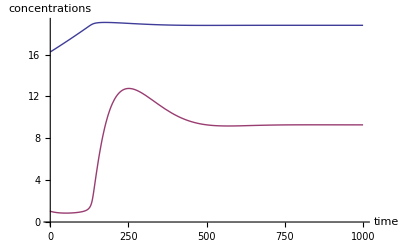

```mathematica
ClearAll[solt]
solt[PARS_]:=Module[{solTMP,minAAsyn,rcrit},
solTMP=NDSolve[
Join[sys,init]/.PARS,
vars,
{t,0,tmax},
Method->"StiffnessSwitching"
];
Flatten[{solTMP,PARS}]
]
(*Usage*)
sol = solt[pars];
Plot[Evaluate[{r[t],ppGpp[t]}/.sol],
{t,0,1000},
AxesLabel->{"time","concentrations"}
]
```

```mathematica
ClearAll[ss]
(*Use this function to calculate the steady state of the system. It first approximates this by evolving the system using solt, and than uses FindRoot to solve the system numerically.*)
ss[PARS_]:=Module[{tsolTEMP,aaguess,taaguess,ppGppguess,rguess,solTEMP,minAAsyn,rcrit},
tsolTEMP=solt[PARS];
aaguess=Flatten[{#,Max[#[tmax]/.tsolTEMP,10*$MachineEpsilon],$MachineEpsilon,∞}]&/@aaSpecies;
taaguess=Flatten[{#,
Max[10*$MachineEpsilon,Min[#[tmax]/.tsolTEMP,(τ1*r[tmax]-$MachineEpsilon)/.tsolTEMP/.PARS]],
$MachineEpsilon,
τ1*rmax/.tsolTEMP/.PARS}]&/@taaSpecies;
ppGppguess={Flatten[{ppGpp,(ppGpp[tmax]/.tsolTEMP),$MachineEpsilon,∞}]};
rguess={Flatten[{r,Min[r[tmax]/.tsolTEMP,.99*rmax/.PARS],$MachineEpsilon,rmax/.PARS}]};
solTEMP=FindRoot[
Thread[0==sys⟦All,2⟧]/.x_[t]->x/.PARS,
Join[aaguess,taaguess,ppGppguess,rguess]];
Flatten[{
solTEMP,
relations/.x_[t]->x/.solTEMP/.PARS,
jR->(vR/.relations/.x_[t]->x/.solTEMP/.PARS)
}]//N
]
ss[pars]//TableForm;
```

```mathematica
(*Compare to optimum (see above)*)
```

```mathematica
r/.opt
r/.ss[pars]
```

ReplaceAll::reps: {opt} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

r/.opt

18.7982

```mathematica
(drate/.ss[pars]/.pars)/(drate/.opt)(*Doubling rate, relative to optimum*)
```

ReplaceAll::reps: {opt} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

1.70586/((3600 krib r)/(bm (1+(f11 κrta)/taa11+(f12 κrta)/taa12+(f13 κrta)/taa13+(f14 κrta)/taa14+(f15 κrta)/taa15+(f16 κrta)/taa16+(f17 κrta)/taa17+(f18 κrta)/taa18+(f19 κrta)/taa19+(f2 κrta)/taa2+(f20 κrta)/taa20+(f3 κrta)/taa3+(f4 κrta)/taa4+(f5 κrta)/taa5+(f6 κrta)/taa6+(f7 κrta)/taa7+(f8 κrta)/taa8+(f9 κrta)/taa9+(f11 tf11 κrta)/(taa11 κrt)+(f12 tf12 κrta)/(taa12 κrt)+(f13 tf13 κrta)/(taa13 κrt)+(f14 tf14 κrta)/(taa14 κrt)+(f15 tf15 κrta)/(taa15 κrt)+(f16 tf16 κrta)/(taa16 κrt)+(f17 tf17 κrta)/(taa17 κrt)+(f18 tf18 κrta)/(taa18 κrt)+(f19 tf19 κrta)/(taa19 κrt)+(f2 tf2 κrta)/(taa2 κrt)+(f20 tf20 κrta)/(taa20 κrt)+(f3 tf3 κrta)/(taa3 κrt)+(f4 tf4 κrta)/(taa4 κrt)+(f5 tf5 κrta)/(taa5 κrt)+(f6 tf6 κrta)/(taa6 κrt)+(f7 tf7 κrta)/(taa7 κrt)+(f8 tf8 κrta)/(taa8 κrt)+(f9 tf9 κrta)/(taa9 κrt)+(f1 (tf1+κrt) κrta)/(taa1 κrt)+(f10 (tf10+κrt) κrta)/(taa10 κrt)) Log[2])/.opt)

```mathematica
(*Lower and higher nutrient quality*)
parsLowNutrient =pars/.Thread[ Thread[(kn/.appendAllI)->_]->Thread[(kn/.appendAllI)->.5*(kn/.appendAllI/.pars)] ];
parsHighNutrient =pars/. Thread[Thread[(kn/.appendAllI)->_]->Thread[(kn/.appendAllI)->2*(kn/.appendAllI/.pars)] ];
```

```mathematica
steadystates = {
{drate,r/rmax}/.ss[parsLowNutrient]/.parsLowNutrient,
{drate,r/rmax}/.ss[pars]/.pars,
{drate,r/rmax}/.ss[parsHighNutrient]/.parsHighNutrient}
```

{{1.0032,0.165689},{1.70586,0.231356},{2.61143,0.334248}}

```mathematica
optima = {
{drate,r/rmax}/.optimum[parsLowNutrient]/.parsLowNutrient,
{drate,r/rmax}/.optimum[pars]/.pars,
{drate,r/rmax}/.optimum[parsHighNutrient]/.parsHighNutrient}
```

ReplaceAll::reps: {optimum[{e1 → 0.05, kn1 → 0.088347, kIa1 → 100, sTot1 → 1, ks1 → 100, kMaa1 → 100, kMtf1 → 1, krib → 20, κrta → 1, κrt → 500, kRelA → 75, RelAtot → 0.0666667, kDRelA → 0.26, vSpoTSynt → 0.001, kSpoTdeg → 0.0231049, vInitMax → 2000, rnapF → 1., kMrrn → 20, kIppGpp → 1., nppGpp → 1., γmax → 1., τ1 → 0.5, f1 → 0.05, « 6 », kIa2 → 100, sTot2 → 1, ks2 → 100, kMaa2 → 100, kMtf2 → 1, τ2 → 0.5, f2 → 0.05, e3 → 0.05, kn3 → 0.107507, kIa3 → 100, sTot3 → 1, ks3 → 100, kMaa3 → 100, kMtf3 → 1, τ3 → 0.5, f3 → 0.05, e4 → 0.05, kn4 → 0.0802649, kIa4 → 100, sTot4 → 1, ks4 → 100, « 148 »}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {optimum[{0.05 → 0.05, 0.088347 → 0.088347, 100 → 100, 1 → 1, 100 → 100, 100 → 100, 1 → 1, 20 → 20, 1 → 1, 500 → 500, 75 → 75, 0.0666667 → 0.0666667, 0.26 → 0.26, 0.001 → 0.001, 0.0231049 → 0.0231049, 2000 → 2000, 1. → 1., 20 → 20, 1. → 1., 1. → 1., 1. → 1., « 9 », 1 → 1, 100 → 100, 100 → 100, 1 → 1, 0.5 → 0.5, 0.05 → 0.05, 0.05 → 0.05, 0.107507 → 0.107507, 100 → 100, 1 → 1, 100 → 100, 100 → 100, 1 → 1, 0.5 → 0.5, 0.05 → 0.05, 0.05 → 0.05, 0.0802649 → 0.0802649, 100 → 100, 1 → 1, 100 → 100, « 148 »}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {optimum[{e1 → 0.05, kn1 → 0.176694, kIa1 → 100, sTot1 → 1, ks1 → 100, kMaa1 → 100, kMtf1 → 1, krib → 20, κrta → 1, κrt → 500, kRelA → 75, RelAtot → 0.0666667, kDRelA → 0.26, vSpoTSynt → 0.001, kSpoTdeg → 0.0231049, vInitMax → 2000, rnapF → 1., kMrrn → 20, kIppGpp → 1., nppGpp → 1., γmax → 1., τ1 → 0.5, f1 → 0.05, « 6 », kIa2 → 100, sTot2 → 1, ks2 → 100, kMaa2 → 100, kMtf2 → 1, τ2 → 0.5, f2 → 0.05, e3 → 0.05, kn3 → 0.215015, kIa3 → 100, sTot3 → 1, ks3 → 100, kMaa3 → 100, kMtf3 → 1, τ3 → 0.5, f3 → 0.05, e4 → 0.05, kn4 → 0.16053, kIa4 → 100, sTot4 → 1, ks4 → 100, « 148 »}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

{{(0.103874 r)/(1+0.05/taa11+0.05/taa12+0.05/taa13+0.05/taa14+0.05/taa15+0.05/taa16+0.05/taa17+0.05/taa18+0.05/taa19+0.05/taa2+0.05/taa20+0.05/taa3+0.05/taa4+0.05/taa5+0.05/taa6+0.05/taa7+0.05/taa8+0.05/taa9+(0.0001 (500+tf1))/taa1+(0.0001 (500+tf10))/taa10+(0.0001 tf11)/taa11+(0.0001 tf12)/taa12+(0.0001 tf13)/taa13+(0.0001 tf14)/taa14+(0.0001 tf15)/taa15+(0.0001 tf16)/taa16+(0.0001 tf17)/taa17+(0.0001 tf18)/taa18+(0.0001 tf19)/taa19+(0.0001 tf2)/taa2+(0.0001 tf20)/taa20+(0.0001 tf3)/taa3+(0.0001 tf4)/taa4+(0.0001 tf5)/taa5+(0.0001 tf6)/taa6+(0.0001 tf7)/taa7+(0.0001 tf8)/taa8+(0.0001 tf9)/taa9),0.0123074 r}/.optimum[{0.05→0.05,0.088347→0.088347,100→100,1→1,100→100,100→100,1→1,20→20,1→1,500→500,75→75,0.0666667→0.0666667,0.26→0.26,0.001→0.001,0.0231049→0.0231049,2000→2000,1.→1.,20→20,1.→1.,1.→1.,1.→1.,0.5→0.5,0.05→0.05,1.×10^6→1.×10^6,12307.3→12307.3,300→300,81.2523→81.2523,0.05→0.05,0.0852362→0.0852362,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.107507→0.107507,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.0802649→0.0802649,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.0770039→0.0770039,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.116126→0.116126,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.0944858→0.0944858,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.101205→0.101205,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.110724→0.110724,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.087578→0.087578,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.109465→0.109465,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.0946252→0.0946252,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.0912506→0.0912506,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.0843986→0.0843986,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.0890864→0.0890864,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.0817787→0.0817787,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.120281→0.120281,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.117354→0.117354,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.119429→0.119429,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.0962763→0.0962763,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05}],{(0.103874 r)/(1+0.05/taa11+0.05/taa12+0.05/taa13+0.05/taa14+0.05/taa15+0.05/taa16+0.05/taa17+0.05/taa18+0.05/taa19+0.05/taa2+0.05/taa20+0.05/taa3+0.05/taa4+0.05/taa5+0.05/taa6+0.05/taa7+0.05/taa8+0.05/taa9+(0.0001 (500+tf1))/taa1+(0.0001 (500+tf10))/taa10+(0.0001 tf11)/taa11+(0.0001 tf12)/taa12+(0.0001 tf13)/taa13+(0.0001 tf14)/taa14+(0.0001 tf15)/taa15+(0.0001 tf16)/taa16+(0.0001 tf17)/taa17+(0.0001 tf18)/taa18+(0.0001 tf19)/taa19+(0.0001 tf2)/taa2+(0.0001 tf20)/taa20+(0.0001 tf3)/taa3+(0.0001 tf4)/taa4+(0.0001 tf5)/taa5+(0.0001 tf6)/taa6+(0.0001 tf7)/taa7+(0.0001 tf8)/taa8+(0.0001 tf9)/taa9),0.0123074 r}/.optimum[{0.05→0.05,0.176694→0.176694,100→100,1→1,100→100,100→100,1→1,20→20,1→1,500→500,75→75,0.0666667→0.0666667,0.26→0.26,0.001→0.001,0.0231049→0.0231049,2000→2000,1.→1.,20→20,1.→1.,1.→1.,1.→1.,0.5→0.5,0.05→0.05,1.×10^6→1.×10^6,12307.3→12307.3,300→300,81.2523→81.2523,0.05→0.05,0.170472→0.170472,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.215015→0.215015,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.16053→0.16053,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.154008→0.154008,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.232252→0.232252,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.188972→0.188972,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.202409→0.202409,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.221447→0.221447,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.175156→0.175156,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.218931→0.218931,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.18925→0.18925,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.182501→0.182501,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.168797→0.168797,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.178173→0.178173,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.163557→0.163557,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.240562→0.240562,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.234708→0.234708,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.238857→0.238857,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.192553→0.192553,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05}],{(0.103874 r)/(1+0.05/taa11+0.05/taa12+0.05/taa13+0.05/taa14+0.05/taa15+0.05/taa16+0.05/taa17+0.05/taa18+0.05/taa19+0.05/taa2+0.05/taa20+0.05/taa3+0.05/taa4+0.05/taa5+0.05/taa6+0.05/taa7+0.05/taa8+0.05/taa9+(0.0001 (500+tf1))/taa1+(0.0001 (500+tf10))/taa10+(0.0001 tf11)/taa11+(0.0001 tf12)/taa12+(0.0001 tf13)/taa13+(0.0001 tf14)/taa14+(0.0001 tf15)/taa15+(0.0001 tf16)/taa16+(0.0001 tf17)/taa17+(0.0001 tf18)/taa18+(0.0001 tf19)/taa19+(0.0001 tf2)/taa2+(0.0001 tf20)/taa20+(0.0001 tf3)/taa3+(0.0001 tf4)/taa4+(0.0001 tf5)/taa5+(0.0001 tf6)/taa6+(0.0001 tf7)/taa7+(0.0001 tf8)/taa8+(0.0001 tf9)/taa9),0.0123074 r}/.optimum[{0.05→0.05,0.353388→0.353388,100→100,1→1,100→100,100→100,1→1,20→20,1→1,500→500,75→75,0.0666667→0.0666667,0.26→0.26,0.001→0.001,0.0231049→0.0231049,2000→2000,1.→1.,20→20,1.→1.,1.→1.,1.→1.,0.5→0.5,0.05→0.05,1.×10^6→1.×10^6,12307.3→12307.3,300→300,81.2523→81.2523,0.05→0.05,0.340945→0.340945,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.43003→0.43003,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.32106→0.32106,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.308016→0.308016,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.464504→0.464504,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.377943→0.377943,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.404818→0.404818,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.442895→0.442895,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.350312→0.350312,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.437862→0.437862,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.378501→0.378501,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.365002→0.365002,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.337594→0.337594,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.356346→0.356346,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.327115→0.327115,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.481124→0.481124,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.469417→0.469417,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.477715→0.477715,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05,0.05→0.05,0.385105→0.385105,100→100,1→1,100→100,100→100,1→1,0.5→0.5,0.05→0.05}]}

ReplaceAll::reps: {optimum[{0.05 → 0.05, 0.088347 → 0.088347, 100. → 100., 1. → 1., 100. → 100., 100. → 100., 1. → 1., 20. → 20., 1. → 1., 500. → 500., 75. → 75., 0.0666667 → 0.0666667, 0.26 → 0.26, 0.001 → 0.001, 0.0231049 → 0.0231049, 2000. → 2000., « 19 », 0.05 → 0.05, 0.05 → 0.05, 0.107507 → 0.107507, 100. → 100., 1. → 1., 100. → 100., 100. → 100., 1. → 1., 0.5 → 0.5, 0.05 → 0.05, 0.05 → 0.05, 0.0802649 → 0.0802649, 100. → 100., 1. → 1., 100. → 100., « 148 »}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {optimum[{0.05 → 0.05, 0.176694 → 0.176694, 100. → 100., 1. → 1., 100. → 100., 100. → 100., 1. → 1., 20. → 20., 1. → 1., 500. → 500., 75. → 75., 0.0666667 → 0.0666667, 0.26 → 0.26, 0.001 → 0.001, 0.0231049 → 0.0231049, 2000. → 2000., « 19 », 0.05 → 0.05, 0.05 → 0.05, 0.215015 → 0.215015, 100. → 100., 1. → 1., 100. → 100., 100. → 100., 1. → 1., 0.5 → 0.5, 0.05 → 0.05, 0.05 → 0.05, 0.16053 → 0.16053, 100. → 100., 1. → 1., 100. → 100., « 148 »}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {optimum[{0.05 → 0.05, 0.353388 → 0.353388, 100. → 100., 1. → 1., 100. → 100., 100. → 100., 1. → 1., 20. → 20., 1. → 1., 500. → 500., 75. → 75., 0.0666667 → 0.0666667, 0.26 → 0.26, 0.001 → 0.001, 0.0231049 → 0.0231049, 2000. → 2000., 1. → 1., « 18 », 0.05 → 0.05, 0.05 → 0.05, 0.43003 → 0.43003, 100. → 100., 1. → 1., 100. → 100., 100. → 100., 1. → 1., 0.5 → 0.5, 0.05 → 0.05, 0.05 → 0.05, 0.32106 → 0.32106, 100. → 100., 1. → 1., 100. → 100., « 148 »}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

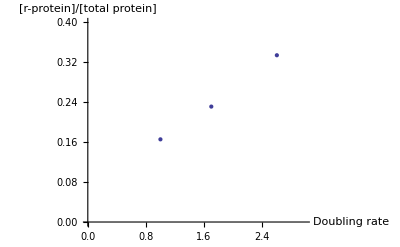

```mathematica
ListPlot[{steadystates,optima},
PlotRange->{{0,3},{0,0.4}},
AxesLabel->{"Doubling rate","[r-protein]/[total protein]"}
]
```

```mathematica
(*The calculatations below show that κrt and vSpoTSynt can be changed by an order of magnutide in either direction without affecting the model outcome.*)
```

```mathematica
ssLowkrt=ss[pars/.Rule[κrt->_,κrt->50]];
optLowkrt=optimum[pars/.Rule[κrt->_,κrt->50]];
(drate/.ssLowkrt/.pars)/(drate/.optLowkrt)
```

ReplaceAll::reps: {optimum[{e1 → 0.05, kn1 → 0.176694, kIa1 → 100, sTot1 → 1, ks1 → 100, kMaa1 → 100, kMtf1 → 1, krib → 20, κrta → 1, κrt → 50, kRelA → 75, RelAtot → 0.0666667, kDRelA → 0.26, vSpoTSynt → 0.001, kSpoTdeg → 0.0231049, vInitMax → 2000, rnapF → 1., kMrrn → 20, kIppGpp → 1., nppGpp → 1., γmax → 1., τ1 → 0.5, f1 → 0.05, « 6 », kIa2 → 100, sTot2 → 1, ks2 → 100, kMaa2 → 100, kMtf2 → 1, τ2 → 0.5, f2 → 0.05, e3 → 0.05, kn3 → 0.215015, kIa3 → 100, sTot3 → 1, ks3 → 100, kMaa3 → 100, kMtf3 → 1, τ3 → 0.5, f3 → 0.05, e4 → 0.05, kn4 → 0.16053, kIa4 → 100, sTot4 → 1, ks4 → 100, « 148 »}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

1.66442/((3600 krib r)/(bm (1+(f11 κrta)/taa11+(f12 κrta)/taa12+(f13 κrta)/taa13+(f14 κrta)/taa14+(f15 κrta)/taa15+(f16 κrta)/taa16+(f17 κrta)/taa17+(f18 κrta)/taa18+(f19 κrta)/taa19+(f2 κrta)/taa2+(f20 κrta)/taa20+(f3 κrta)/taa3+(f4 κrta)/taa4+(f5 κrta)/taa5+(f6 κrta)/taa6+(f7 κrta)/taa7+(f8 κrta)/taa8+(f9 κrta)/taa9+(f11 tf11 κrta)/(taa11 κrt)+(f12 tf12 κrta)/(taa12 κrt)+(f13 tf13 κrta)/(taa13 κrt)+(f14 tf14 κrta)/(taa14 κrt)+(f15 tf15 κrta)/(taa15 κrt)+(f16 tf16 κrta)/(taa16 κrt)+(f17 tf17 κrta)/(taa17 κrt)+(f18 tf18 κrta)/(taa18 κrt)+(f19 tf19 κrta)/(taa19 κrt)+(f2 tf2 κrta)/(taa2 κrt)+(f20 tf20 κrta)/(taa20 κrt)+(f3 tf3 κrta)/(taa3 κrt)+(f4 tf4 κrta)/(taa4 κrt)+(f5 tf5 κrta)/(taa5 κrt)+(f6 tf6 κrta)/(taa6 κrt)+(f7 tf7 κrta)/(taa7 κrt)+(f8 tf8 κrta)/(taa8 κrt)+(f9 tf9 κrta)/(taa9 κrt)+(f1 (tf1+κrt) κrta)/(taa1 κrt)+(f10 (tf10+κrt) κrta)/(taa10 κrt)) Log[2])/.optimum[{e1→0.05,kn1→0.176694,kIa1→100,sTot1→1,ks1→100,kMaa1→100,kMtf1→1,krib→20,κrta→1,κrt→50,kRelA→75,RelAtot→0.0666667,kDRelA→0.26,vSpoTSynt→0.001,kSpoTdeg→0.0231049,vInitMax→2000,rnapF→1.,kMrrn→20,kIppGpp→1.,nppGpp→1.,γmax→1.,τ1→0.5,f1→0.05,bm→1.×10^6,nARib→12307.3,nAmet→300,rmax→81.2523,e2→0.05,kn2→0.170472,kIa2→100,sTot2→1,ks2→100,kMaa2→100,kMtf2→1,τ2→0.5,f2→0.05,e3→0.05,kn3→0.215015,kIa3→100,sTot3→1,ks3→100,kMaa3→100,kMtf3→1,τ3→0.5,f3→0.05,e4→0.05,kn4→0.16053,kIa4→100,sTot4→1,ks4→100,kMaa4→100,kMtf4→1,τ4→0.5,f4→0.05,e5→0.05,kn5→0.154008,kIa5→100,sTot5→1,ks5→100,kMaa5→100,kMtf5→1,τ5→0.5,f5→0.05,e6→0.05,kn6→0.232252,kIa6→100,sTot6→1,ks6→100,kMaa6→100,kMtf6→1,τ6→0.5,f6→0.05,e7→0.05,kn7→0.188972,kIa7→100,sTot7→1,ks7→100,kMaa7→100,kMtf7→1,τ7→0.5,f7→0.05,e8→0.05,kn8→0.202409,kIa8→100,sTot8→1,ks8→100,kMaa8→100,kMtf8→1,τ8→0.5,f8→0.05,e9→0.05,kn9→0.221447,kIa9→100,sTot9→1,ks9→100,kMaa9→100,kMtf9→1,τ9→0.5,f9→0.05,e10→0.05,kn10→0.175156,kIa10→100,sTot10→1,ks10→100,kMaa10→100,kMtf10→1,τ10→0.5,f10→0.05,e11→0.05,kn11→0.218931,kIa11→100,sTot11→1,ks11→100,kMaa11→100,kMtf11→1,τ11→0.5,f11→0.05,e12→0.05,kn12→0.18925,kIa12→100,sTot12→1,ks12→100,kMaa12→100,kMtf12→1,τ12→0.5,f12→0.05,e13→0.05,kn13→0.182501,kIa13→100,sTot13→1,ks13→100,kMaa13→100,kMtf13→1,τ13→0.5,f13→0.05,e14→0.05,kn14→0.168797,kIa14→100,sTot14→1,ks14→100,kMaa14→100,kMtf14→1,τ14→0.5,f14→0.05,e15→0.05,kn15→0.178173,kIa15→100,sTot15→1,ks15→100,kMaa15→100,kMtf15→1,τ15→0.5,f15→0.05,e16→0.05,kn16→0.163557,kIa16→100,sTot16→1,ks16→100,kMaa16→100,kMtf16→1,τ16→0.5,f16→0.05,e17→0.05,kn17→0.240562,kIa17→100,sTot17→1,ks17→100,kMaa17→100,kMtf17→1,τ17→0.5,f17→0.05,e18→0.05,kn18→0.234708,kIa18→100,sTot18→1,ks18→100,kMaa18→100,kMtf18→1,τ18→0.5,f18→0.05,e19→0.05,kn19→0.238857,kIa19→100,sTot19→1,ks19→100,kMaa19→100,kMtf19→1,τ19→0.5,f19→0.05,e20→0.05,kn20→0.192553,kIa20→100,sTot20→1,ks20→100,kMaa20→100,kMtf20→1,τ20→0.5,f20→0.05}])

```mathematica
ssHighkrt=ss[pars/.Rule[κrt->_,κrt->5000]];
optHighkrt=optimum[pars/.Rule[κrt->_,κrt->5000]];
(drate/.ssHighkrt/.pars)/(drate/.optHighkrt)
```

ReplaceAll::reps: {optimum[{e1 → 0.05, kn1 → 0.176694, kIa1 → 100, sTot1 → 1, ks1 → 100, kMaa1 → 100, kMtf1 → 1, krib → 20, κrta → 1, κrt → 5000, kRelA → 75, RelAtot → 0.0666667, kDRelA → 0.26, vSpoTSynt → 0.001, kSpoTdeg → 0.0231049, vInitMax → 2000, rnapF → 1., kMrrn → 20, kIppGpp → 1., nppGpp → 1., γmax → 1., τ1 → 0.5, f1 → 0.05, « 6 », kIa2 → 100, sTot2 → 1, ks2 → 100, kMaa2 → 100, kMtf2 → 1, τ2 → 0.5, f2 → 0.05, e3 → 0.05, kn3 → 0.215015, kIa3 → 100, sTot3 → 1, ks3 → 100, kMaa3 → 100, kMtf3 → 1, τ3 → 0.5, f3 → 0.05, e4 → 0.05, kn4 → 0.16053, kIa4 → 100, sTot4 → 1, ks4 → 100, « 148 »}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

1.63006/((3600 krib r)/(bm (1+(f11 κrta)/taa11+(f12 κrta)/taa12+(f13 κrta)/taa13+(f14 κrta)/taa14+(f15 κrta)/taa15+(f16 κrta)/taa16+(f17 κrta)/taa17+(f18 κrta)/taa18+(f19 κrta)/taa19+(f2 κrta)/taa2+(f20 κrta)/taa20+(f3 κrta)/taa3+(f4 κrta)/taa4+(f5 κrta)/taa5+(f6 κrta)/taa6+(f7 κrta)/taa7+(f8 κrta)/taa8+(f9 κrta)/taa9+(f11 tf11 κrta)/(taa11 κrt)+(f12 tf12 κrta)/(taa12 κrt)+(f13 tf13 κrta)/(taa13 κrt)+(f14 tf14 κrta)/(taa14 κrt)+(f15 tf15 κrta)/(taa15 κrt)+(f16 tf16 κrta)/(taa16 κrt)+(f17 tf17 κrta)/(taa17 κrt)+(f18 tf18 κrta)/(taa18 κrt)+(f19 tf19 κrta)/(taa19 κrt)+(f2 tf2 κrta)/(taa2 κrt)+(f20 tf20 κrta)/(taa20 κrt)+(f3 tf3 κrta)/(taa3 κrt)+(f4 tf4 κrta)/(taa4 κrt)+(f5 tf5 κrta)/(taa5 κrt)+(f6 tf6 κrta)/(taa6 κrt)+(f7 tf7 κrta)/(taa7 κrt)+(f8 tf8 κrta)/(taa8 κrt)+(f9 tf9 κrta)/(taa9 κrt)+(f1 (tf1+κrt) κrta)/(taa1 κrt)+(f10 (tf10+κrt) κrta)/(taa10 κrt)) Log[2])/.optimum[{e1→0.05,kn1→0.176694,kIa1→100,sTot1→1,ks1→100,kMaa1→100,kMtf1→1,krib→20,κrta→1,κrt→5000,kRelA→75,RelAtot→0.0666667,kDRelA→0.26,vSpoTSynt→0.001,kSpoTdeg→0.0231049,vInitMax→2000,rnapF→1.,kMrrn→20,kIppGpp→1.,nppGpp→1.,γmax→1.,τ1→0.5,f1→0.05,bm→1.×10^6,nARib→12307.3,nAmet→300,rmax→81.2523,e2→0.05,kn2→0.170472,kIa2→100,sTot2→1,ks2→100,kMaa2→100,kMtf2→1,τ2→0.5,f2→0.05,e3→0.05,kn3→0.215015,kIa3→100,sTot3→1,ks3→100,kMaa3→100,kMtf3→1,τ3→0.5,f3→0.05,e4→0.05,kn4→0.16053,kIa4→100,sTot4→1,ks4→100,kMaa4→100,kMtf4→1,τ4→0.5,f4→0.05,e5→0.05,kn5→0.154008,kIa5→100,sTot5→1,ks5→100,kMaa5→100,kMtf5→1,τ5→0.5,f5→0.05,e6→0.05,kn6→0.232252,kIa6→100,sTot6→1,ks6→100,kMaa6→100,kMtf6→1,τ6→0.5,f6→0.05,e7→0.05,kn7→0.188972,kIa7→100,sTot7→1,ks7→100,kMaa7→100,kMtf7→1,τ7→0.5,f7→0.05,e8→0.05,kn8→0.202409,kIa8→100,sTot8→1,ks8→100,kMaa8→100,kMtf8→1,τ8→0.5,f8→0.05,e9→0.05,kn9→0.221447,kIa9→100,sTot9→1,ks9→100,kMaa9→100,kMtf9→1,τ9→0.5,f9→0.05,e10→0.05,kn10→0.175156,kIa10→100,sTot10→1,ks10→100,kMaa10→100,kMtf10→1,τ10→0.5,f10→0.05,e11→0.05,kn11→0.218931,kIa11→100,sTot11→1,ks11→100,kMaa11→100,kMtf11→1,τ11→0.5,f11→0.05,e12→0.05,kn12→0.18925,kIa12→100,sTot12→1,ks12→100,kMaa12→100,kMtf12→1,τ12→0.5,f12→0.05,e13→0.05,kn13→0.182501,kIa13→100,sTot13→1,ks13→100,kMaa13→100,kMtf13→1,τ13→0.5,f13→0.05,e14→0.05,kn14→0.168797,kIa14→100,sTot14→1,ks14→100,kMaa14→100,kMtf14→1,τ14→0.5,f14→0.05,e15→0.05,kn15→0.178173,kIa15→100,sTot15→1,ks15→100,kMaa15→100,kMtf15→1,τ15→0.5,f15→0.05,e16→0.05,kn16→0.163557,kIa16→100,sTot16→1,ks16→100,kMaa16→100,kMtf16→1,τ16→0.5,f16→0.05,e17→0.05,kn17→0.240562,kIa17→100,sTot17→1,ks17→100,kMaa17→100,kMtf17→1,τ17→0.5,f17→0.05,e18→0.05,kn18→0.234708,kIa18→100,sTot18→1,ks18→100,kMaa18→100,kMtf18→1,τ18→0.5,f18→0.05,e19→0.05,kn19→0.238857,kIa19→100,sTot19→1,ks19→100,kMaa19→100,kMtf19→1,τ19→0.5,f19→0.05,e20→0.05,kn20→0.192553,kIa20→100,sTot20→1,ks20→100,kMaa20→100,kMtf20→1,τ20→0.5,f20→0.05}])

```mathematica
ssHignvSpoT=ss[pars/.Rule[vSpoTSynt->_,vSpoTSynt->0.01]];
ssLowvSpoT=ss[pars/.Rule[vSpoTSynt->_,vSpoTSynt->0.0001]];
(drate/.ssHignvSpoT/.pars)/(drate/.opt)
(drate/.ssLowvSpoT/.pars)/(drate/.opt)
```

ReplaceAll::reps: {opt} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

1.70627/((3600 krib r)/(bm (1+(f11 κrta)/taa11+(f12 κrta)/taa12+(f13 κrta)/taa13+(f14 κrta)/taa14+(f15 κrta)/taa15+(f16 κrta)/taa16+(f17 κrta)/taa17+(f18 κrta)/taa18+(f19 κrta)/taa19+(f2 κrta)/taa2+(f20 κrta)/taa20+(f3 κrta)/taa3+(f4 κrta)/taa4+(f5 κrta)/taa5+(f6 κrta)/taa6+(f7 κrta)/taa7+(f8 κrta)/taa8+(f9 κrta)/taa9+(f11 tf11 κrta)/(taa11 κrt)+(f12 tf12 κrta)/(taa12 κrt)+(f13 tf13 κrta)/(taa13 κrt)+(f14 tf14 κrta)/(taa14 κrt)+(f15 tf15 κrta)/(taa15 κrt)+(f16 tf16 κrta)/(taa16 κrt)+(f17 tf17 κrta)/(taa17 κrt)+(f18 tf18 κrta)/(taa18 κrt)+(f19 tf19 κrta)/(taa19 κrt)+(f2 tf2 κrta)/(taa2 κrt)+(f20 tf20 κrta)/(taa20 κrt)+(f3 tf3 κrta)/(taa3 κrt)+(f4 tf4 κrta)/(taa4 κrt)+(f5 tf5 κrta)/(taa5 κrt)+(f6 tf6 κrta)/(taa6 κrt)+(f7 tf7 κrta)/(taa7 κrt)+(f8 tf8 κrta)/(taa8 κrt)+(f9 tf9 κrta)/(taa9 κrt)+(f1 (tf1+κrt) κrta)/(taa1 κrt)+(f10 (tf10+κrt) κrta)/(taa10 κrt)) Log[2])/.opt)

ReplaceAll::reps: {opt} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

1.70582/((3600 krib r)/(bm (1+(f11 κrta)/taa11+(f12 κrta)/taa12+(f13 κrta)/taa13+(f14 κrta)/taa14+(f15 κrta)/taa15+(f16 κrta)/taa16+(f17 κrta)/taa17+(f18 κrta)/taa18+(f19 κrta)/taa19+(f2 κrta)/taa2+(f20 κrta)/taa20+(f3 κrta)/taa3+(f4 κrta)/taa4+(f5 κrta)/taa5+(f6 κrta)/taa6+(f7 κrta)/taa7+(f8 κrta)/taa8+(f9 κrta)/taa9+(f11 tf11 κrta)/(taa11 κrt)+(f12 tf12 κrta)/(taa12 κrt)+(f13 tf13 κrta)/(taa13 κrt)+(f14 tf14 κrta)/(taa14 κrt)+(f15 tf15 κrta)/(taa15 κrt)+(f16 tf16 κrta)/(taa16 κrt)+(f17 tf17 κrta)/(taa17 κrt)+(f18 tf18 κrta)/(taa18 κrt)+(f19 tf19 κrta)/(taa19 κrt)+(f2 tf2 κrta)/(taa2 κrt)+(f20 tf20 κrta)/(taa20 κrt)+(f3 tf3 κrta)/(taa3 κrt)+(f4 tf4 κrta)/(taa4 κrt)+(f5 tf5 κrta)/(taa5 κrt)+(f6 tf6 κrta)/(taa6 κrt)+(f7 tf7 κrta)/(taa7 κrt)+(f8 tf8 κrta)/(taa8 κrt)+(f9 tf9 κrta)/(taa9 κrt)+(f1 (tf1+κrt) κrta)/(taa1 κrt)+(f10 (tf10+κrt) κrta)/(taa10 κrt)) Log[2])/.opt)